```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]<>"\\Code\\OutputData"];
```

## Визуализация сингулярных интегралов

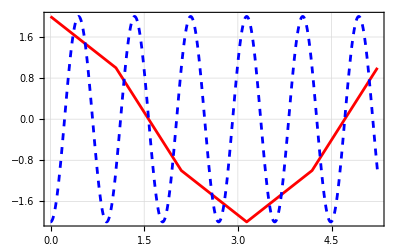

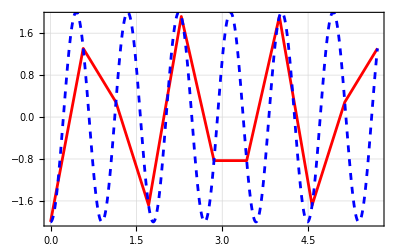

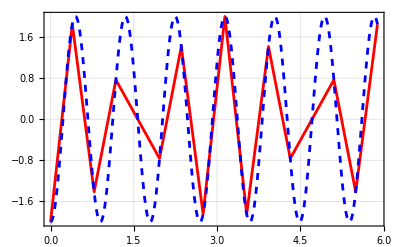

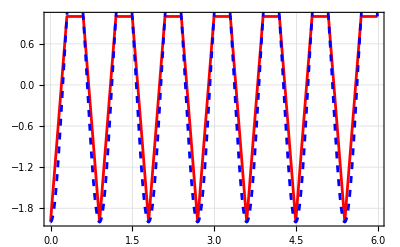

```mathematica
data1 = Import["SingularTest3_1.txt", "Table"];
data2 = Import["SingularTest3_2.txt", "Table"];
data3 = Import["SingularTest3_3.txt", "Table"];
data4 = Import["SingularTest3_4.txt", "Table"];

sol = -2 Cos[7 ϕ];
SingPlot[data_, sol_] := Module[{plotdata, plotsol},
plotdata = ListPlot[Table[{data[[1]][[i]],data[[2]][[i]]},{i,1,Length@data[[1]]}], Joined->True, PlotStyle -> Red];
plotsol = Plot[sol, {ϕ, data[[1]][[1]], data[[1]][[-1]]}, PlotStyle -> {Blue, Dashed}];
Show[plotdata, plotsol,ImageSize->{400,250},AspectRatio->1/GoldenRatio, Frame->True,AxesOrigin->{0,0}, GridLines->Automatic]
]
SingPlot[data1, sol]
SingPlot[data2, sol]
SingPlot[data3, sol]
SingPlot[data4, sol]
```